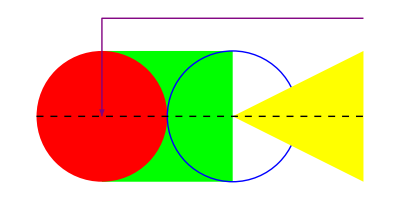

```mathematica
Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]
```

Initial Conditions:

```mathematica
basis={{1,0},{0.5,Sqrt[3]/2}}; (* A basis generating the lattice points. Length equal to dimension of lattice.*)
rowLength[n_Integer]:=If[EvenQ[n],{n/2,n/2},{(n+1)/2,(n-1)/2}]; (*First value is odd trangles*)
r=rowLength[15]; (* Specifies how many "odd" and "even" triangles are in our graphic. *)
c={0,0,0,0,0,0,0,1,0,0,0,1,0,0,0}; (* Initial conditions. *)
```

Triangular Array Case:

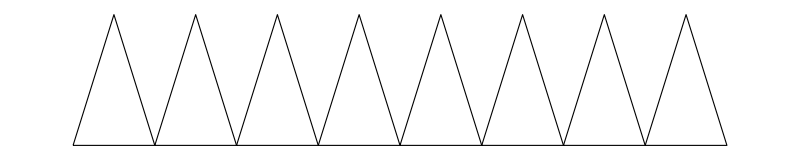

```mathematica
oddTriangles[basis_,rowLength_,initialConditions_]:=
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*i+1]]]],EdgeForm[Black],Triangle[{i*basis[[1]]+{0,0},i*basis[[1]]+basis[[1]],i*basis[[1]]+basis[[2]]}]},
{i,0,rowLength[[1]]-1}]; (* Generates the "odd" traingles that can then be interpreted as Graphics objects. *)
Graphics[oddTriangles[basis,r,c],ImageSize->100*r[[1]]]
```

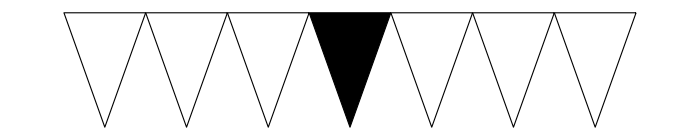

```mathematica
evenTriangles[basis_,rowLength_,initialConditions_]:=
Table[
{FaceForm[GrayLevel[1-initialConditions[[2*(i+1)]]]],EdgeForm[Black],
Triangle[{(i+1)*basis[[1]]+basis[[2]],i*basis[[1]]+basis[[1]],i*basis[[1]]+basis[[2]]}]},
{i,0,rowLength[[2]]-1}];(* Generates the "even" traingles that can then be interpreted as Graphics objects. *)
Graphics[evenTriangles[basis,r,c],ImageSize->100*r[[2]]]
```

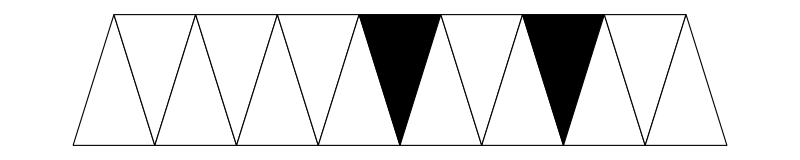

```mathematica
triangleCA[basis_,rowLength_,initialConditions_]:=
Graphics[Riffle[
oddTriangles[basis,rowLength,initialConditions],evenTriangles[basis,rowLength,initialConditions]
],ImageSize->100*r[[1]]]; (* Combines the "odd" and "even" triangle lists and makes a graphic for them. *)
gen1=triangleCA[basis,r,c]
```

```mathematica
triangleCAList[basis_,rowLength_,initialConditions_]:=
Riffle[
oddTriangles[basis,rowLength,initialConditions],evenTriangles[basis,rowLength,initialConditions]
];
triangleCAList[basis,r,c]
```

{{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{0,0},{1,0},{0.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1.5,(√3)/2},{1,0},{0.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{1,0},{2,0},{1.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2.5,(√3)/2},{2,0},{1.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{2,0},{3,0},{2.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3.5,(√3)/2},{3,0},{2.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{3,0},{4,0},{3.5,(√3)/2}}]},{FaceForm[GrayLevel[0]],EdgeForm[GrayLevel[0]],Triangle[{{4.5,(√3)/2},{4,0},{3.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{4,0},{5,0},{4.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5.5,(√3)/2},{5,0},{4.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{5,0},{6,0},{5.5,(√3)/2}}]},{FaceForm[GrayLevel[0]],EdgeForm[GrayLevel[0]],Triangle[{{6.5,(√3)/2},{6,0},{5.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{6,0},{7,0},{6.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{7.5,(√3)/2},{7,0},{6.5,(√3)/2}}]},{FaceForm[GrayLevel[1]],EdgeForm[GrayLevel[0]],Triangle[{{7,0},{8,0},{7.5,(√3)/2}}]}}

New generation rule:

```mathematica
rule=30;
neighboorCount=3;
ruleTable[rule_Integer,neighboorCount_Integer]:=Reverse[PadLeft[IntegerDigits[rule,2],2^neighboorCount]]; (* Given a number and Moore neighborhood size generates a rule table. *)
```

```mathematica
nextStep[initialConditions_]:=Table[
ruleTable[rule,neighboorCount][[FromDigits[
If[i<neighboorCount/2,PadLeft[Take[initialConditions,{1,i+Floor[neighboorCount/2]}],neighboorCount],If[i>Total[r]-neighboorCount/2,PadRight[Take[initialConditions,{i-Floor[neighboorCount/2],Total[r]}],neighboorCount],Take[initialConditions,{i-Floor[neighboorCount/2],i+Floor[neighboorCount/2]}]]],2]+1]]
,{i,1,Length[initialConditions]}]; (*Generates the state at time t+1 given state at time t. *)
```

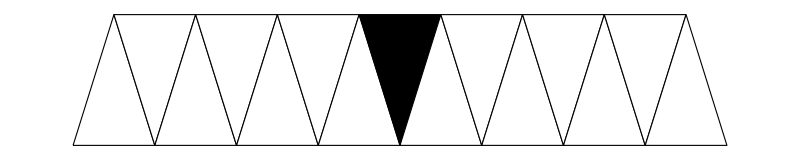

```mathematica
gen1
```

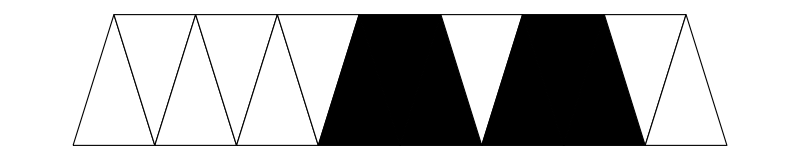

```mathematica
gen2=triangleCA[basis,r,nextStep[c]]
```

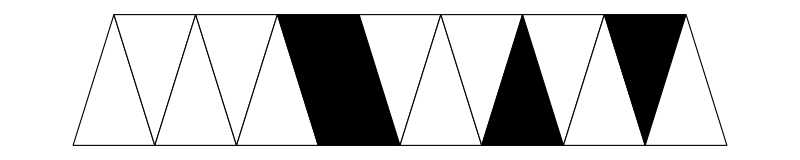

```mathematica
gen3=triangleCA[basis,r,nextStep[nextStep[c]]]
```

```mathematica
Graphics[triangleCAList[basis,r,c]]
```

-Graphics-

```mathematica
Row[Table[i^2,{i,0,10}]]
```

0149162536496481100

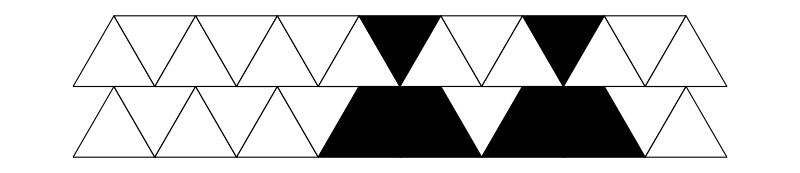

```mathematica
Graphics[{triangleCAList[basis,r,c],Translate[triangleCAList[basis,r,nextStep[c]],{0,-Sqrt[3]/2}]},ImageSize->100*r[[1]]]
```